# NG 21 P13 Генетическое кодирование, генетические операции

Бельская Екатерина, 
2 курс, 5 группа

```mathematica
SetDirectory@NotebookDirectory[];
Get["NG21P13Problem.mx","NG21P13"]
```

```mathematica
Troubles
```

CompiledFunction[…]

```mathematica
Range[-1,1,0.5]
Lighter@ColorData["GreenPinkTones",#]&/@%
ColorData["GreenPinkTones","Range"]
```

{-1.,-0.5,0.,0.5,1.}

{RGBColor[0.3333333333333333, 0.4949266666666666, 0.3488161333333333],RGBColor[0.3333333333333333, 0.4949266666666666, 0.3488161333333333],RGBColor[0.3333333333333333, 0.4949266666666666, 0.3488161333333333],RGBColor[0.9491866666666667, 0.9336773333333334, 0.948518],RGBColor[0.49621799999999994, 0.36752373333333327, 0.49417333333333335]}

{0,1}

Так как у ColorDataFunction аргумент лежит в диапазоне от 0 до 1, то нужно привести значения к этому диапазону (будем делить на 10, так как максимальное значение 9.65113)

```mathematica
MinMax@Array[Troubles[{#1,#2,#3,#4}]&,{10,10,10,10},{{0,100},{0,100},{0,10},{0,360}}]
```

{0.651804,9.65113}

```mathematica
P=MapThread[List,{RandomReal[{0,100},100],RandomReal[{0,100},100],RandomReal[{0,10},100],RandomReal[{0,360},100]}];
```

```mathematica
ClearAll[ShowPhenotype];
ShowPhenotype[{x_,y_,F_,a_}]:={Darker@ColorData["GreenPinkTones",Troubles[{x,y,F,a}]/10],Point[{x,y}],
Arrow[{{x,y},{x+F Cos [a Degree],y+F Sin[a Degree]}}]}
ShowPhenotype[pop_]:=Graphics[ShowPhenotype[#]&/@pop,Frame->True,GridLines->Automatic]
```

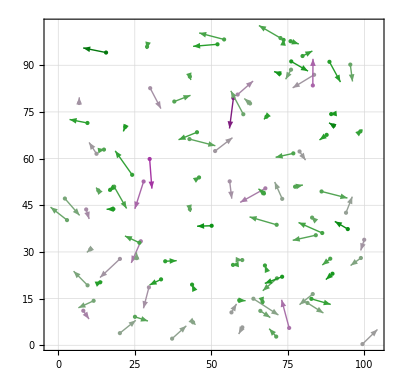

```mathematica
ShowPhenotype[P]
```

## 2. Квантование

x:[0,100,0.1]≈1000<1024 = 2^10→10 
y:[0,100,0.1]≈1000<1024 = 2^10→10 
F:[0,10,0.01]≈1000<1024 = 2^10→10 
α:[0,360,1]≈360< 512 = 2^9→9

```mathematica
ClearAll[AnalogToDigital, DigitalToAnalog];
AnalogToDigital[{from_,to_},bits_Integer]:=Round[ (# - from- 2^(-1-bits))/(2^-bits(to-from))]&;
DigitalToAnalog[{from_,to_},bits_Integer]:= Round[(to-from)(from  + # 2^-bits+2^(-1-bits) ),0.1]&;
```

```mathematica
AnalogToDigital[{0,10},10]/@Range[0,10]
```

{0,102,205,307,410,512,614,717,819,922,1024}

## 3. Код Грея

нужно представить число в битовой форме и сдвинуть на один бит с помощью исключающего или

```mathematica
n=IntegerDigits[12,2,6]
```

{0,0,1,1,0,0}

```mathematica
nn=IntegerDigits[BitShiftRight[12,1],2,6]
```

{0,0,0,1,1,0}

```mathematica
BitXor[n,nn]
```

{0,0,1,0,1,0}

```mathematica
ClearAll[GrayTable, ToGray,FromGray];

ToGray[n_]:=Module[{num=IntegerDigits[n,2],numShifted},numShifted=IntegerDigits[BitShiftRight[n,1],2];
numShifted=PadLeft[numShifted,Length@num];BitXor[num,numShifted]];
ToGray[n_Integer,len_Integer]:=Module[{num=IntegerDigits[n,2,len],numShifted},numShifted=IntegerDigits[BitShiftRight[n,1],2,len];
BitXor[num,numShifted]];
GrayTable=ToGray[#]&/@ Range[0,1024];
FromGray[g_]:=  Fold[BitXor,0,FixedPointList[BitShiftRight,FromDigits[g,2]]]
```

```mathematica
FromGray[ToGray[15,6]]
```

15

```mathematica
FromDigits[ToGray[15,6],2]
```

8

```mathematica
ToGray[#,10]&/@Range[0,10]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

```mathematica
StringJoin[ToString/@{0,0,0,0,0,0,1,1,1,1}]
```

0000001111

```mathematica
ToGray[15]
```

1000

```mathematica
ToGray[15,6]
```

001000

```mathematica
FromGray[ToGray[15,6]]
```

15

## 4. Генетическое кодирование

```mathematica
ClearAll[PhenotypeToGenotype,GenotypeToPhenotype];
PhenotypeToGenotype[{x_,y_,F_,α_}]:=Flatten@MapThread[ToGray[#1,#2]&,{MapThread[AnalogToDigital[{0,#1},#2][#3]&,{{100,100,10,360},{10,10,10,9} ,{x,y,F,α}}],{10,10,10,9}}];
GenotypeToPhenotype[chromosome_]:= N@MapThread[DigitalToAnalog[{0,#1},Length[#2]][FromGray[#2]]&,{{100,100,10,360},Partition[chromosome,UpTo[10]]}];
```

```mathematica
PhenotypeToGenotype[{32,28,10,200}]
```

{0,1,1,1,1,0,1,1,0,0,0,1,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,1,0}

```mathematica
Length@%
```

39

## 5. Популяция

```mathematica
pP= RandomReal[{0,1},{20,4}].{{100,0,0,0},{0,100,0,0},{0,0,10,0},{0,0,0,360}};
```

```mathematica
pG =PhenotypeToGenotype/@ pP;
```

Можем заметить погрешность

```mathematica
GenotypeToPhenotype/@pG
pP
```

{{62.7,61.4,0.1,188.1},{19.4,60.1,2.8,226.8},{42.8,52.4,7.1,224.6},{3.9,64.2,5.,69.3},{25.7,95.4,2.7,178.9},{64.9,73.6,9.7,215.5},{26.6,8.6,5.8,99.5},{25.3,91.3,3.5,69.3},{50.,84.4,0.2,332.2},{86.6,49.8,4.9,268.2},{96.3,66.1,2.7,252.1},{55.5,77.8,4.6,46.8},{43.3,28.8,8.9,70.7},{32.3,68.1,3.7,6.},{26.3,88.3,6.1,43.2},{25.2,6.6,6.3,60.1},{42.1,91.5,0.1,182.5},{86.6,54.1,5.5,183.2},{85.9,89.5,5.3,352.6},{20.5,46.,7.7,110.7}}

{{62.6595,61.3689,0.0459305,187.998},{19.2958,60.0666,2.76994,226.751},{42.7678,52.3823,7.06348,224.018},{3.81062,64.1309,5.03472,68.9538},{25.6696,95.3163,2.7103,178.916},{64.8017,73.5826,9.69325,214.969},{26.5189,8.5593,5.75848,98.9011},{25.3391,91.2599,3.51675,68.8295},{50.0466,84.4089,0.206417,331.964},{86.5597,49.7433,4.89558,268.129},{96.2524,65.9909,2.66576,251.414},{55.505,77.758,4.60115,46.0912},{43.2499,28.7541,8.91497,70.2524},{32.2734,68.0646,3.66165,5.60113},{26.2481,88.3012,6.05761,43.2233},{25.166,6.50129,6.24694,59.8848},{42.1182,91.4169,0.0856137,182.321},{86.563,54.0411,5.476,182.558},{85.8254,89.4859,5.26996,352.31},{20.4108,46.0328,7.67692,110.649}}

```mathematica
ClearAll[ShowGenotype];

ShowGenotype[pop_List]:= ArrayPlot[pop]
```

```mathematica
ShowGenotype[pG]
```

-Graphics-

## 6. Мутация

Случайный бит будет заменяться на противоположный

```mathematica
ex={0,1,0,0};
```

```mathematica
ex⟦3⟧=ex⟦3⟧/.{0->1,0->1}
ex
```

1

{0,1,1,0}

```mathematica
GenOper["Mutation",individual_]:=Module[{bit=RandomInteger[{1,39}],m=individual},m⟦bit⟧=m⟦bit⟧/.{0->1,1->0};m]
```

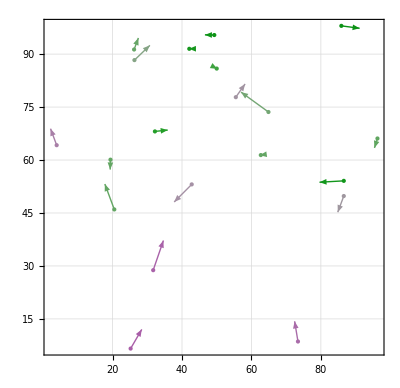

```mathematica
ShowPhenotype[GenotypeToPhenotype[#]&/@(GenOper["Mutation",#]&/@pG)]
```

## 7. Инверсия

Пример для сдвига на длина/2

```mathematica
pG⟦1⟧
Partition[%,UpTo[Ceiling[Length[%]/2]]]
Reverse@%
Join@@%
```

{1,1,1,1,0,0,0,0,1,1,1,1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,1,1,1,0}

{{1,1,1,1,0,0,0,0,1,1,1,1,0,1,0,0,1,1,1,0},{0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,1,1,1,0}}

{{0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,1,1,1,0},{1,1,1,1,0,0,0,0,1,1,1,1,0,1,0,0,1,1,1,0}}

{0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,1,1,1,0,1,1,1,1,0,0,0,0,1,1,1,1,0,1,0,0,1,1,1,0}

Сдвигаем на рандомное число бит

```mathematica
GenOper["Inversion",individual_]:= RotateRight[individual,RandomInteger[{1,39}]]
```

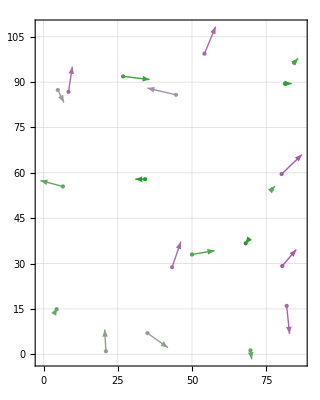

```mathematica
ShowPhenotype[GenotypeToPhenotype[#]&/@(GenOper["Inversion",#]&/@pG)]
```

## 8. Скрещивание

Какая - то часть генотипа одной особи + часть генотипа другой особи

```mathematica
parent1=pG⟦1⟧
```

{1,1,1,1,0,0,0,0,1,1,1,1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,1,1,1,0}

```mathematica
parent2=pG⟦2⟧
```

{0,0,1,0,1,0,0,1,0,1,1,1,0,1,0,1,0,1,0,0,0,1,1,0,0,1,0,0,1,0,1,1,1,1,0,0,0,1,1}

```mathematica
pos=RandomInteger[{1,39}]
```

34

```mathematica
Append[parent1⟦1;;pos⟧,parent2⟦pos+1;;⟧]//Flatten
```

{1,1,1,1,0,0,0,0,1,1,1,1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,1,1}

```mathematica
GenOper["Crossover",parent1_, parent2_]:=  Module[{pos=RandomInteger[39]},Append[parent1⟦1;;pos⟧,parent2⟦pos+1;;⟧]//Flatten]
```

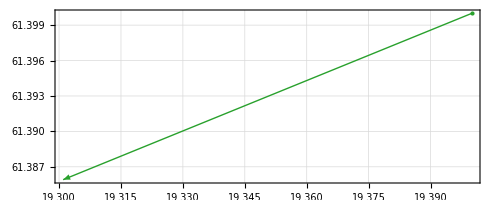

```mathematica
ShowPhenotype[{GenotypeToPhenotype@GenOper["Crossover",{pG⟦1⟧,pG⟦2⟧}]}]
```

```mathematica
list=RandomInteger[{1,20},{2,10}]
```

{{19,18,16,15,18,8,14,8,1,10},{11,7,6,9,19,8,2,16,15,6}}

```mathematica
MapThread[GenOper["Crossover",{pG⟦#1⟧,pG⟦#2⟧}]&,list]
```

{{1,0,1,1,0,1,1,0,0,0,1,0,0,1,0,1,1,1,1,0,1,1,0,0,0,1,1,0,0,1,1,1,1,0,1,0,1,0,1},{0,1,1,0,0,1,1,0,0,0,0,0,0,1,1,1,0,1,0,0,1,1,0,1,1,0,1,0,0,1,1,1,0,0,0,0,1,1,0},{1,1,1,1,0,0,0,0,1,1,0,0,0,1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1},{1,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,1,1,0,1,0,0,0,0,1,0,0,0,1,1},{1,0,1,1,0,1,1,0,0,0,1,0,0,1,0,1,1,1,0,1,1,1,0,0,1,0,1,0,0,1,1,1,0,0,0,0,1,1,0},{0,1,1,0,0,0,0,0,1,0,1,0,0,1,1,1,0,1,0,1,0,1,1,1,0,1,1,1,0,0,0,0,1,0,1,0,0,1,1},{0,0,1,0,1,0,0,1,0,1,1,1,0,1,0,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0},{0,1,1,0,0,0,0,0,1,0,1,0,0,1,1,1,0,1,0,1,0,1,1,1,0,1,1,1,0,0,0,0,1,0,1,0,0,1,1},{1,1,1,1,0,0,0,0,1,1,1,1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,1,1},{1,0,1,1,0,1,0,1,0,0,1,1,1,0,0,0,1,0,0,1,1,0,0,0,0,1,0,0,0,1,1,1,0,1,0,1,0,1,1}}

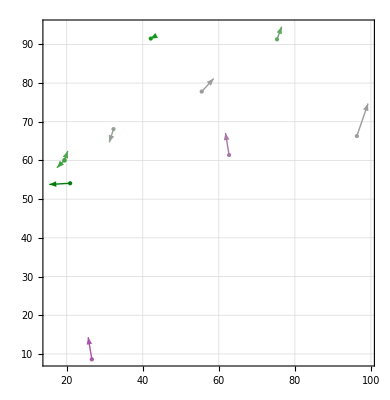

```mathematica
ShowPhenotype[GenotypeToPhenotype[#]&/@MapThread[GenOper["Crossover",{pG⟦#1⟧,pG⟦#2⟧}]&,RandomInteger[{1,20},{2,10}]]]
```